This is a code for bootstrapping the single matrix model

## loop equations bootstrap V=1/2 ϕ^2+ 1/4 g ϕ^4

```mathematica
c2[g_]:=Module[{a=Sqrt[1/(6 g)((1+12g)^(1/2)-1)]},1/3 a^2(4-a^2)];
c2[0]=1;
```

#### some analytics

```mathematica
c2[g_]:=Module[{a=Sqrt[1/(6 g)((1+12g)^(1/2)-1)]},1/3 a^2(4-a^2)];
c4[g_]:=Module[{a=Sqrt[1/(6 g)((1+12g)^(1/2)-1)]},1/2 a^4(6-2a^2)];
c2p[x_]:=1-2 x+9 x^2-54 x^3;
c4p[x_]:=2-9 x+54 x^2-378 x^3;
```

```mathematica
ρ[g_,λ_]:=Module[{a2=2/(3 g)(-1+Sqrt[1+12 g])},-I/(2π)(g λ^2+g a2/2+1)Sqrt[λ^2-a2] ]
```

#### A view of the peninsula

```mathematica
Clear[g]
```

```mathematica
Subscript[t, 0]=1;Subscript[t, 1]=0;max=71;(*Odd number*)
Do[
Subscript[t, k+2]=0;
Subscript[t, k+3]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]-Subscript[t, k+1])],{k,Range[1,max,2]}
];
expressions=Table[ Evaluate[ Subscript[t, k]],{k,Range[2,max+1,2]} ];
tk=expressions[[-21]];
tk1=expressions[[-11]];
tk2=expressions[[-1]];
```

General::munfl: (-1.39958×10^-7)^50 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.39958×10^-7)^51 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.39958×10^-7)^52 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

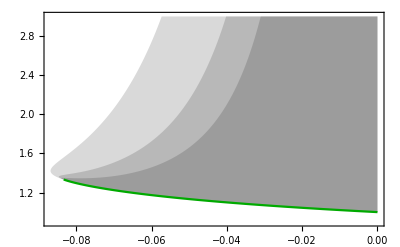
-Graphics-tr M^2g

```mathematica
p0=Plot[{Solve[tk==0][[1,1,2]],Solve[tk==0][[2,1,2]]},{g,-0.09,0},PlotPoints->200,PlotRange->{0.9,3},PlotStyle->{Opacity[0],Opacity[0]},Evaluate@plotsci,Filling->{1->{2}},FillingStyle->{Opacity[0.15],Gray}];
p1=Plot[{Solve[tk1==0][[1,1,2]],Solve[tk1==0][[2,1,2]]},{g,-0.09,0},PlotPoints->200,PlotRange->{0.9,3},PlotStyle->{Opacity[0],Opacity[0]},Evaluate@plotsci,Filling->{1->{2}},FillingStyle->{Opacity[0.15],Gray}];
p2=Plot[{Solve[tk2==0][[1,1,2]],Solve[tk2==0][[2,1,2]],c2[g]},{g,-0.09,0},PlotPoints->200,PlotRange->{0.9,3},PlotStyle->{Opacity[0],Opacity[0],{Darker@Green,Thickness[0.004]}},Evaluate@plotsci,Filling->{1->{2}},FillingStyle->{Opacity[0.15],Gray}];
gg=Show[p0,p1,p2];
Labeled[gg,{"tr M^2","g"},{Left,Bottom},labelsci]
```

```mathematica
Manipulate[Plot[tk2/.{g->gg},{Subscript[t, 2],0,1.5}],{gg,-0.08,1.0}]
```

```mathematica
tk2/.{g->3.0,Subscript[t, 2]->0.7}
```

9.45694

```mathematica
Expand[(X-a)^4]
```

a^4-4 a^3 X+6 a^2 X^2-4 a X^3+X^4

```mathematica
m={{Subscript[t, 2j],Subscript[t, j+k]},{Subscript[t, j+k],Subscript[t, 2k]}}
```

{{t_(2 j),t_(j+k)},{t_(j+k),t_(2 k)}}

```mathematica
Eigenvalues[m]//FullSimplify
```

{1/2 (t_(2 j)+t_(2 k)-√((t_(2 j)-t_(2 k))^2+4 t_(j+k)^2)),1/2 (t_(2 j)+t_(2 k)+√((t_(2 j)-t_(2 k))^2+4 t_(j+k)^2))}

```mathematica
1/4 (1+x2m-√(1-2 x2m+x2m^2+4 xm^2))^2//Expand
```

1/2+x2m^2/2+xm^2-1/2 √(1-2 x2m+x2m^2+4 xm^2)-1/2 x2m √(1-2 x2m+x2m^2+4 xm^2)

#### Fingers plot

```mathematica
Subscript[t, 0]=1;Subscript[t, 1]=0;max=71;(*Odd number*)
Do[
Subscript[t, k+2]=0;
Subscript[t, k+3]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]-Subscript[t, k+1])],{k,Range[1,max,2]}
];
expressions=Table[ Evaluate[ Subscript[t, k]],{k,Range[2,max+1,2]} ];
tk2=expressions[[-1]];
tk22=expressions[[-3]];
```

t_2

```mathematica
tk6=expressions[[4]];
```

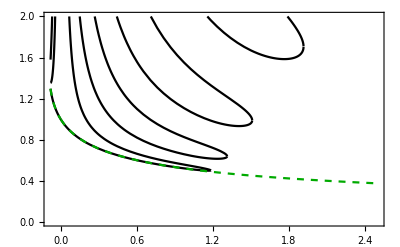

```mathematica
p=Plot[{Solve[tk22==0][[;;,1,2]],c2[g]},{g,-0.08,2.5},PerformanceGoal->"Quality",PlotRange->{0,2}, Evaluate@plotsci,PlotStyle->{Black,{Darker@Green,Dashed}},Filling->{4->{2}}]
```

```mathematica
Show[p,AspectRatio-> 0.6180339887498948]
```

-Graphics-

```mathematica
ColorData[97,"ColorList"][[1]]
```

RGBColor[0.368417, 0.506779, 0.709798]

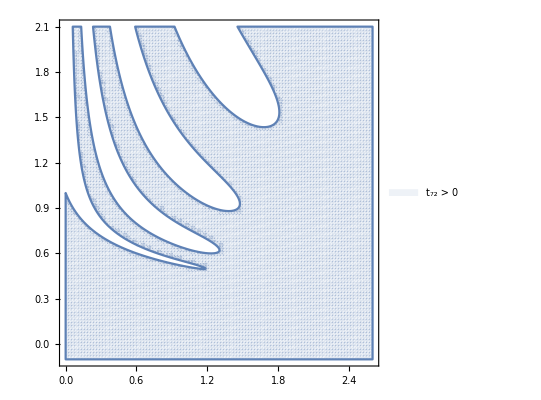

```mathematica
rp72=RegionPlot[{tk2>0},{g,0,2.6},{Subscript[t, 2],-0.1,2.1},PlotPoints->100,PlotLegends->{"t_72 > 0","t_68 > 0","t_8 > 0"},PlotStyle->Opacity[0.1]]
```

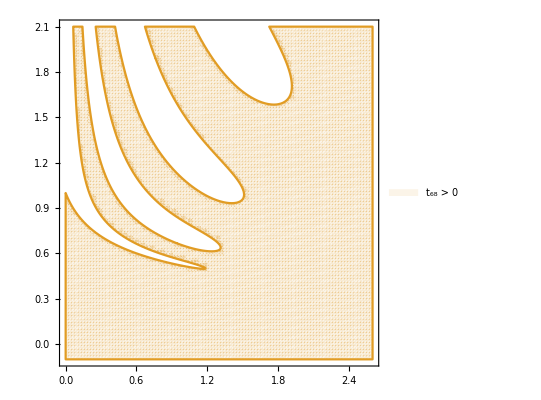

```mathematica
rp68=RegionPlot[{tk22>0},{g,0,2.6},{Subscript[t, 2],-0.1,2.1},PlotPoints->100,PlotLegends->{"t_68 > 0","t_8 > 0"},
PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],Opacity[0.1]]},BoundaryStyle->ColorData[97,"ColorList"][[2]]
]
```

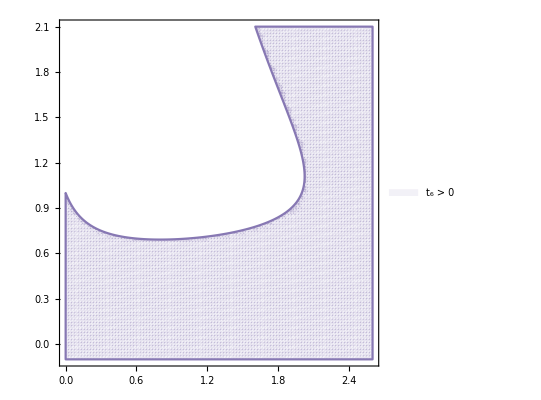

```mathematica
rp6=RegionPlot[{tk6>0},{g,0,2.6},{Subscript[t, 2],-0.1,2.1},PlotPoints->100,PlotLegends->{"t_6 > 0"},
PlotStyle->{Directive[ColorData[97,"ColorList"][[5]],Opacity[0.1]]},BoundaryStyle->ColorData[97,"ColorList"][[5]]
]
```

```mathematica
Labeled[Show[rp72,rp68,rp6,exact,PlotRange->{{0.05,2.5},{0,2.0}},plotsci,AspectRatio->0.6180339887498948],"tr M^2",Left,labelsci]
```

-Graphics-tr M^2

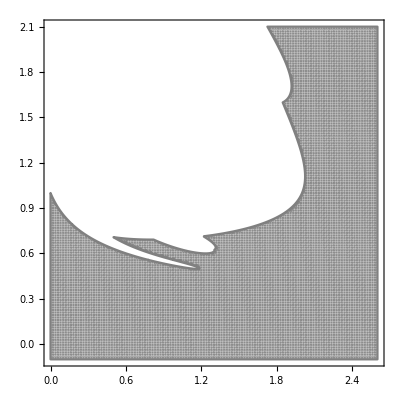

```mathematica
rpInt=RegionPlot[{tk2>0&&tk6>0&&tk22>0},{g,0,2.6},{Subscript[t, 2],-0.1,2.1},PlotPoints->200,PlotStyle->{Opacity[0.3],Gray},BoundaryStyle->Gray]
```

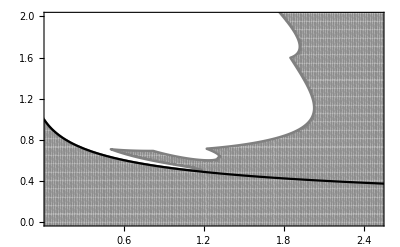
-Graphics-tr M^2g

```mathematica
Labeled[Show[rpInt,exact,PlotRange->{{0.05,2.5},{0,2.0}},plotsci,AspectRatio->0.6180339887498948],{"tr M^2","g"},{Left,Bottom},labelsci]
```

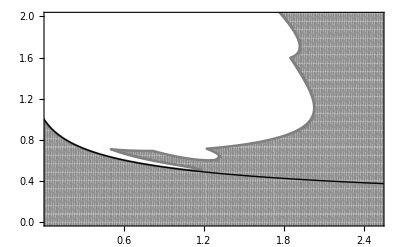

```mathematica
Show[rpInt,exact,PlotRange->{{0.05,2.5},{0,2.0}},plotsci,AspectRatio->0.6180339887498948]
```

```mathematica
Show[rp72,rp68,rp6,exact,PlotRange->{{0.05,2.5},{0,2.0}},plotsci,AspectRatio->0.6180339887498948]
```

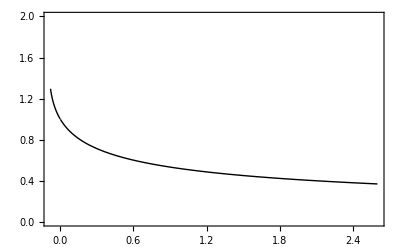

```mathematica
exact=Plot[c2[g],{g,-0.08,2.6},PerformanceGoal->"Quality",PlotRange->{0,2}, Evaluate@plotsci,PlotStyle->{Thick,Black},Filling->{4->{2}}]
```

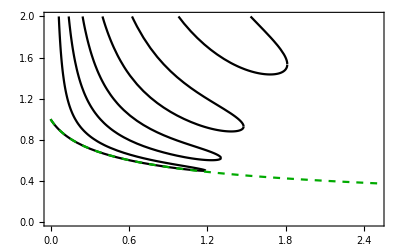
-Graphics-tr M^2g

```mathematica
Labeled[p,{"tr M^2","g" },{Left,Bottom},labelsci]
```

#### Fancy method

here we do max =10, for just the negative part.

```mathematica
Subscript[t, 0]=1;
Subscript[t, 1]=0;
max=14; (* choose an even number for compatibility with cM *)
(** in this code, Subscript[t, 2] is left as the variable **)
Do[
Subscript[t, k+2]=0;
Subscript[t, k+3]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]-Subscript[t, k+1])],{k,Range[1,max-3,2]}];
```

```mathematica
cM=Table[Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
res=1/400;
dat2=Table[{j*res,detM=Det[cM/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,-34,-1}];
down2=Transpose@{dat2[[;;,1]],dat2[[;;,2,5]]};
up2=Transpose@{dat2[[;;,1]],dat2[[;;,2,6]]};
down0={{0,1}};
up0={{0,1}};
downn=Sort@Join[down0,down2];
upp=Sort@Join[up0,up2];
(* dat=Delete[dat,3];*)
```

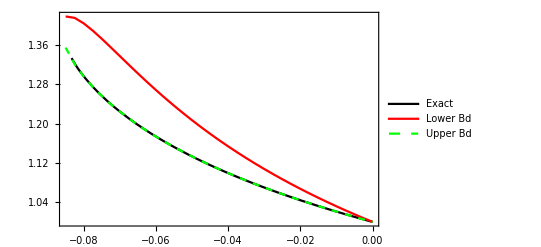
-Graphics-⟨Tr M^2⟩g

```mathematica
Labeled[Show[Plot[{c2[x]},{x,-1/10,0},PlotStyle->{Black},PlotLegends->{"Exact"},GridLines->{{0,-1/12}},PlotRange->All ],ListPlot[{upp,downn},Joined->True,InterpolationOrder->1,PlotStyle->{Red,{Green,Dashed}},PlotLegends->{"Lower Bd"," Upper Bd"}],Evaluate@plotsci],{"⟨Tr M^2⟩","g"},{Left,Bottom},labelsci]
```

here we do max=20.

```mathematica
Subscript[t, 0]=1;
Subscript[t, 1]=0;
max=20; (* choose an even number for compatibility with cM *)
(** in this code, Subscript[t, 2] is left as the variable **)
Do[
Subscript[t, k+2]=0;
Subscript[t, k+3]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]-Subscript[t, k+1])],{k,Range[1,max-3,2]}];
```

```mathematica
cM=Table[g^(j+k)Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
jm=2;
res=1/50;
dat=Table[{j*res,detM=Det[cM/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
res=1/200;
dat2=Table[{j*res,detM=Det[cM/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,-20,-1}];
(* dat=Delete[dat,3];*)
```

```mathematica
up=Transpose@{dat[[;;,1]],dat[[;;,2,9]]};
down=Transpose@{dat[[;;,1]],dat[[;;,2,8]]};
up2=Transpose@{dat2[[;;,1]],dat2[[;;,2,8]]};
down2=Transpose@{dat2[[;;,1]],dat2[[;;,2,7]]};
down0={{0,1}};
up0={{0,1}};
upp=Sort@Join[up,up0,up2];
downn=Sort@Join[down,down0,down2];
```

```mathematica
exact={#,N[c2@#]}&/@upp[[;;,1]];
```

```mathematica
exact[[2]]
```

{-19/200,1.45686-0.107486 ⅈ}

```mathematica
upperr=Table[{exact[[i,1]],upp[[i,2]]-exact[[i,2]]},{i,1,Length@exact}];
downerr=Table[{exact[[i,1]],downn[[i,2]]-exact[[i,2]]},{i,1,Length@exact}];
```

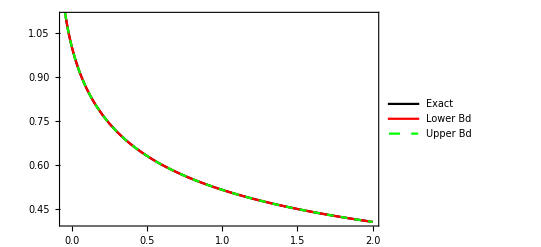
-Graphics-⟨Tr M^2⟩g

```mathematica
Labeled[Show[Plot[{c2[x]},{x,-1/24,2},PlotStyle->{Black},PlotLegends->{"Exact"},GridLines->{{0,-1/12}}],ListPlot[{upp,downn},Joined->True,PlotStyle->{Red,{Green,Dashed}},PlotLegends->{"Lower Bd"," Upper Bd"}],Evaluate@plotsci],{"⟨Tr M^2⟩","g"},{Left,Bottom},labelsci]
```

Nice plots

```mathematica
jm=5;res=1/100;
```

```mathematica
d=4;
dat6=Table[{j*res,detM=Det[cM[[;;d,;;d]]/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
PrependTo[dat7,{0,ConstantArray[1,Length[dat7[[1,2]]]]}];
```

```mathematica
d=5;
dat7=Table[{j*res,detM=Det[cM[[;;d,;;d]]/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
PrependTo[dat7,{0,ConstantArray[1,Length[dat7[[1,2]]]]}];
```

```mathematica
d=6;
dat8=Table[{j*res,detM=Det[cM[[;;d,;;d]]/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
PrependTo[dat8,{0,ConstantArray[1,Length[dat8[[1,2]]]]}];
```

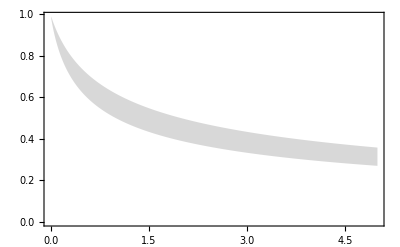

```mathematica
up6=Transpose@{dat6[[;;,1]],dat6[[;;,2,-1]]};
down6=Transpose@{dat6[[;;,1]],dat6[[;;,2,-2]]};
l6=ListPlot[{down6,up6},Joined->True,InterpolationOrder->2,PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Gray,Opacity[0.3]],PerformanceGoal->"Quality",Evaluate@plotsci]
```

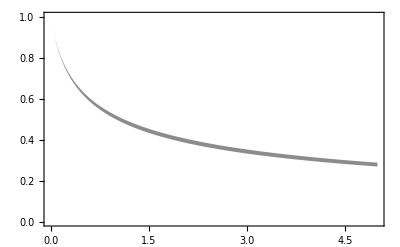

```mathematica
up7=Transpose@{dat7[[;;,1]],dat7[[;;,2,-1]]};
down7=Transpose@{dat7[[;;,1]],dat7[[;;,2,-2]]};
l7=ListPlot[{down7,up7},Joined->True,InterpolationOrder->2,PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Gray,Opacity[0.9]],PerformanceGoal->"Quality",Evaluate@plotsci]
```

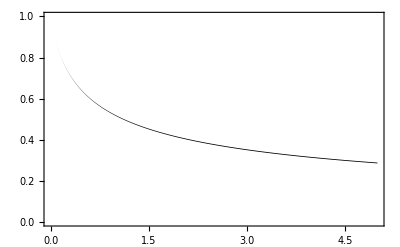

```mathematica
up8=Transpose@{dat8[[;;,1]],dat8[[;;,2,-3]]};
down8=Transpose@{dat8[[;;,1]],dat8[[;;,2,-2]]};
l8=ListPlot[{down8,up8},Joined->True,InterpolationOrder->2,PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Black,PerformanceGoal->"Quality",Evaluate@plotsci]
```

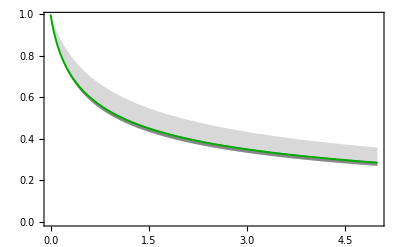
-Graphics-tr M^2g

```mathematica
Labeled[Show[l6,l7,Plot[{c2[x]},{x,0,5},PlotRange->{0,1},PlotStyle->{{Darker@Green,Thickness[0.0035]}},GridLines->{{0,-1/12}}],
Graphics[{Opacity[0],EdgeForm[Thickness[0.0035]],Rectangle[{1,0.48},{1.1,0.53}]}]
],{"tr M^2","g"},{Left,Bottom},labelsci]
```

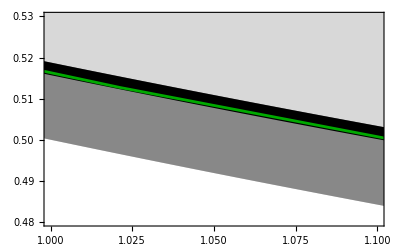
-Graphics-tr M^2g

```mathematica
Labeled[Show[l6,l7,l8,Plot[{c2[x]},{x,0,5},PlotRange->{0,1},PlotStyle->{{Darker@Green,Thickness[0.005]}},GridLines->{{0,-1/12}}],PlotRange->{{1,1.1},{0.48,0.53}}
],{"tr M^2","g"},{Left,Bottom},labelsci]
```

#### Fancy method for cubic

```mathematica
(** please clear the kernel if you have run the above code for the quartic **)
```

```mathematica
Subscript[t, k+3]=1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]-Subscript[t, k+1])
```

```mathematica
ClearAll[t]
```

```mathematica
Subscript[t, 0]=1;max=12; (* choose an even number for compatibility with cM *)
Do[
Subscript[t, k+2]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]-Subscript[t, k+1])],{k,Range[1,max-2,1]}
];
```

```mathematica
max=6;(** must be smaller than previous max **)
cM=Table[g^(j+k)Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
jm=0.27;
res=1/1000;
datsmall=Table[{j*res,detM=Det[cM/.{g->j*res}]/.{Subscript[t, 1]->t2};Normal@NSolve[detM==0,t2][[;;,1,2]]},{j,1,jm/res}];
```

```mathematica
Min@Eigenvalues[cM]/.{g->1/1000,Subscript[t, 1]->-1.0}
```

-5.0251×10^-16

```mathematica
max=8;
cM=Table[g^(j+k)Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
jm=0.27;
res=1/1000;
datmed=Table[{j*res,detM=Det[cM/.{g->j*res}]/.{Subscript[t, 1]->t2};Normal@NSolve[detM==0,t2][[;;,1,2]]},{j,1,jm/res}];
```

```mathematica
cM/.{g->0.21}/.{Subscript[t, 1]->-0.3}//Eigenvalues
```

{1.00896,0.0667906,0.00865766,0.000784676,0.0000334545}

```mathematica
max=12;
cM=Table[g^(j+k)Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
jm=0.24;
res=1/1000;
dat=Table[{j*res,detM=Det[cM/.{g->j*res}]/.{Subscript[t, 1]->t2};Normal@NSolve[detM==0,t2][[;;,1,2]]},{j,1,jm/res}];
AppendTo[dat,{0.2227,detM=Det[cM/.{g->0.2227}]/.{Subscript[t, 1]->t2};Normal@NSolve[detM==0,t2][[;;,1,2]]}];
```

Special critical point

```mathematica
detM=Det[cM/.{g->0.2227}]/.{Subscript[t, 1]->t2};Normal@NSolve[detM==0,t2][[;;,1,2]]
```

{-5.41156,-4.72497-0.08749 ⅈ,-4.72497+0.08749 ⅈ,-4.5931,-4.32951-0.482846 ⅈ,-4.32951+0.482846 ⅈ,-1.77977,-1.24223-2.55036 ⅈ,-1.24223+2.55036 ⅈ,-0.420866-0.237055 ⅈ,-0.420866+0.237055 ⅈ,-0.325571,-0.322279,-0.269172,0.459015}

Checking that we are using the right bounds

```mathematica
Eigenvalues@cM/.{g->0.23,Subscript[t, 1]->-0.33}
```

{-0.000441449,0.000122032,0.00519821,0.0770304,1.01306}

```mathematica
NMinimize[(Eigenvalues[cM][[1]]/.{g->0.23})^2,Subscript[t, 1]]
```

{3.37756×10^-37,{t_1→-0.392937}}

```mathematica
Eigenvalues@cM/.{g->0.23,Subscript[t, 1]->-0.36857066135685873}
```

{0.0000102212,0.00060926,0.0102913,0.0932865,1.0173}

```mathematica
NMaximize[Min@Eigenvalues@cM/.{g->0.23},Subscript[t, 1]]
```

{0.0000102212,{t_1→-0.368571}}

```mathematica
1/Sqrt[12. Sqrt[3]]
```

0.219346

ListPlot::ioproc: {{0.001,-0.999498},{0.002,-0.99899},{0.003,-0.998478},{0.004,-0.997962},{0.005,-0.99744},{0.006,-0.996913},«39»,{0.046,-0.971336},{0.047,-0.970572},{0.048,-0.9698},{0.049,-0.969022},{0.05,-0.968237},«220»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

ListPlot::ioproc: {{0.001,-0.001},{0.002,-0.00200003},{0.003,-0.00300011},{0.004,-0.00400026},{0.005,-0.0050005},{0.006,-0.00600086},«39»,{0.046,-0.0463959},{0.047,-0.0474226},{0.048,-0.0484505},{0.049,-0.0494796},{0.05,-0.0505099},«220»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

ListPlot::iodeg: 2 is not a valid interpolation order specification, or the given order is too high for the input array {{0.21935,0.},{0.21935,-0.4}}.

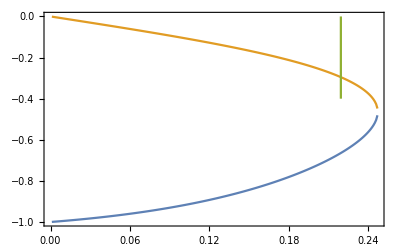
-Graphics-⟨Tr M⟩g

```mathematica
upsmall=Transpose@{datsmall[[;;,1]],datsmall[[;;,2,-2]]};
downsmall=Transpose@{datsmall[[;;,1]],datsmall[[;;,2,-3]]};
Labeled[Show[ListPlot[{downsmall,upsmall,{{0.21935,0},{0.21935,-0.4}}},Joined->True,InterpolationOrder->2],Evaluate@plotsci],{"⟨Tr M⟩","g"},{Left,Bottom},labelsci]
```

ListPlot::ioproc: {{0.001,-0.002},{0.002,-0.00400003},{0.003,-0.00600011},{0.004,-0.00800026},{0.005,-0.0100005},{0.006,-0.0120009},«39»,{0.046,-0.0923824},{0.047,-0.0944075},{0.048,-0.0964337},{0.049,-0.0984609},{0.05,-0.100489},«220»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

ListPlot::ioproc: {{0.001,-0.001},{0.002,-0.00200003},{0.003,-0.00300011},{0.004,-0.00400026},{0.005,-0.0050005},{0.006,-0.00600086},«39»,{0.046,-0.0463961},{0.047,-0.0474228},{0.048,-0.0484507},{0.049,-0.0494799},{0.05,-0.0505103},«220»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

ListPlot::iodeg: 2 is not a valid interpolation order specification, or the given order is too high for the input array {{0.21935,0.},{0.21935,-0.4}}.

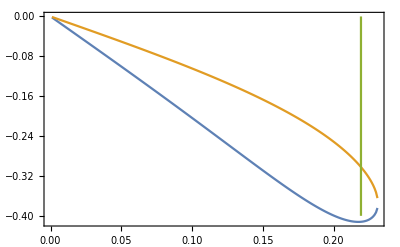
-Graphics-⟨Tr M⟩g

```mathematica
upmed=Transpose@{datmed[[;;,1]],datmed[[;;,2,-2]]};
downmed=Transpose@{datmed[[;;,1]],datmed[[;;,2,-3]]};
Labeled[Show[ListPlot[{downmed,upmed,{{0.21935,0},{0.21935,-0.4}}},Joined->True,InterpolationOrder->2],Evaluate@plotsci],{"⟨Tr M⟩","g"},{Left,Bottom},labelsci]
```

```mathematica
downmed;
```

ListPlot::ioproc: {{0.001,-0.999498},{0.002,-0.99899},{0.003,-0.998478},{0.004,-0.997962},{0.005,-0.99744},{0.006,-0.996913},«39»,{0.046,-0.971336},{0.047,-0.970572},{0.048,-0.9698},{0.049,-0.969022},{0.05,-0.968237},«220»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

ListPlot::ioproc: {{0.001,-0.001},{0.002,-0.00200003},{0.003,-0.00300011},{0.004,-0.00400026},{0.005,-0.0050005},{0.006,-0.00600086},«39»,{0.046,-0.0463959},{0.047,-0.0474226},{0.048,-0.0484505},{0.049,-0.0494796},{0.05,-0.0505099},«220»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

ListPlot::ioproc: {{0.001,-0.002},{0.002,-0.00400003},{0.003,-0.00600011},{0.004,-0.00800026},{0.005,-0.0100005},{0.006,-0.0120009},«39»,{0.046,-0.0923824},{0.047,-0.0944075},{0.048,-0.0964337},{0.049,-0.0984609},{0.05,-0.100489},«220»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

General::stop: Further output of ListPlot::ioproc will be suppressed during this calculation.

ListPlot::iodeg: 2 is not a valid interpolation order specification, or the given order is too high for the input array {{0.21935,0.},{0.21935,-2.}}.

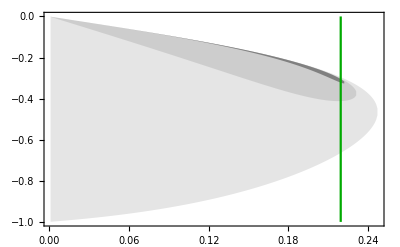
-Graphics-tr Mg_3

```mathematica
up=Transpose@{dat[[;;,1]],dat[[;;,2,-4]]};
down=Transpose@{dat[[;;,1]],dat[[;;,2,-3]]};
Labeled[Show[ListPlot[{downsmall,upsmall,downmed,upmed,down,up,{{0.21935,0},{0.21935,-2}}},Joined->True,PlotRange->{0,-1.0},
PlotStyle->{Opacity[0],Opacity[0],Opacity[0],Opacity[0],Opacity[0],Opacity[0],Darker@Green},Filling->{1->{{2},{Opacity[0.1],Gray}},3->{{4},{Opacity[0.1],Gray}},5->{{6},{Opacity[1],Gray}}},
InterpolationOrder->2],Evaluate@plotsci],{"tr M","g_3"},{Left,Bottom},labelsci]
```

#### null vector calculation

```mathematica
Subscript[t, 0]=1;Subscript[t, 1]=0;max=24;(*Odd number*)
Do[
Subscript[t, k+2]=0;
Subscript[t, k+3]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]-Subscript[t, k+1])],{k,Range[1,max,2]}
];
cM=Table[If[OddQ[j+k],0,g^(j+k)Subscript[t, j+k]],{j,Range[0,max+1]},{k,Range[0,max+1]}];
```

```mathematica
d=8;
mat=cM[[;;d,;;d]]/.{g->1,Subscript[t, 2]->c2[1.0]};
eg=Eigensystem[mat];
nv1=eg[[2,d]];
```

```mathematica
d=12;
mat=cM[[;;d,;;d]]/.{g->1,Subscript[t, 2]->c2[1.0]};
eg2=Eigensystem[mat];
nv2=eg2[[2,d]];
```

```mathematica
ρ[g_,λ_]:=Module[{a2=2/(3 g)(-1+Sqrt[1+12 g])},-I/(2π)(g λ^2+g a2/2+1)Sqrt[λ^2-a2] ]
```

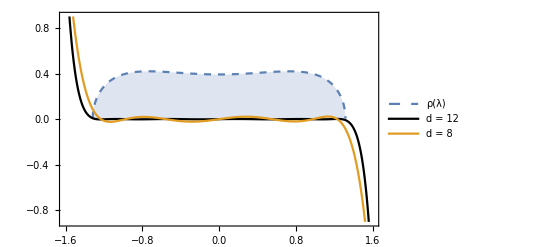
-Graphics-ϕ(λ)λ

```mathematica
Labeled[Plot[{ρ[1,x],(Sum[nv2[[k]] x^(k-1),{k,1,12}]),(Sum[nv1[[k]] x^(k-1),{k,1,8}])},{x,-1.6,1.6},PlotRange->{-0.9,0.9},Evaluate@plotsci,PlotStyle->{{Dashed},Black,ColorData[97,"ColorList"][[2]]},Filling->{1->0},PlotLegends->{"ρ(λ)","d = 12","d = 8"}],{"ϕ(λ)","λ"},{Left,Bottom},labelsci]
```

#### Fancy method with SSB

```mathematica
Clear[g];
Subscript[t, 0]=1;
(*Subscript[t, 1]=0;*)
max=70; (* choose an even number for compatibility with cM *)
Do[
Subscript[t, k+3]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]+Subscript[t, k+1])],{k,Range[0,max-3,1]}
];
```

```mathematica
max=70;
cM=Table[Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
me[t1_,t2_]:=Min@Eigenvalues[cM/.{g->1/16,Subscript[t, 1]->t1,Subscript[t, 2]->t2}]
```

```mathematica
d=10;
mat=cM[[;;d,;;d]]/.{g->1/16,Subscript[t, 2]->16,Subscript[t, 1]->0};
eg=Eigensystem[mat];
nv1=eg[[2,-1]];
nv1=N[nv1,8];
```

```mathematica
d=20;
mat=cM[[;;d,;;d]]/.{g->1/16,Subscript[t, 2]->16,Subscript[t, 1]->0};
eg2=Eigensystem[mat];
nv2=eg2[[2,-1]];
nv2=N[nv2,8];
```

```mathematica
nv2//N
```

{0.,81792.,0.,166448.,0.,-35136.,0.,2619.1,0.,-84.4182,0.,1.}

```mathematica
g=1/16;a2=(1+2 √g)/g;b2=(1-2 √g)/g;
```

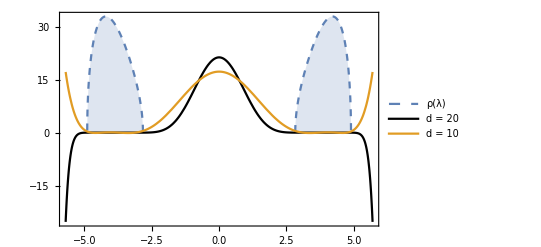
-Graphics-ϕ(λ)λ

```mathematica
Labeled[Plot[{Sqrt[(b2-x^2)(x^2-a2)] Abs[x],-0.5 10^(-9)(Sum[nv2[[k]] x^(k-1),{k,1,Length@nv2}]),0.3 10^(-3)(Sum[nv1[[k]] x^(k-1),{k,1,Length@nv1}])},{x,-5.7,5.7},Evaluate@plotsci,PlotRange->All,PlotStyle->{{Dashed},Black,ColorData[97,"ColorList"][[2]]},Filling->{1->0},PlotLegends->{"ρ(λ)","d = 20","d = 10"}],{"ϕ(λ)","λ"},{Left,Bottom},labelsci]
```

{18.5424,Null}

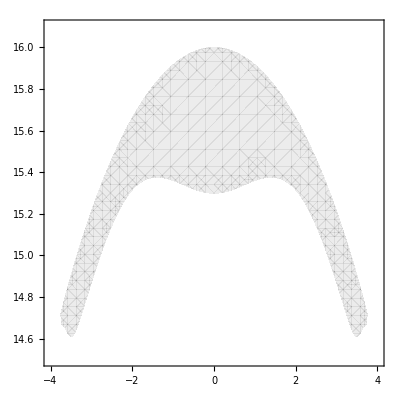

```mathematica
max=16;
cM=Table[Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
me[t1_,t2_]:=Min@Eigenvalues[cM/.{g->1/16,Subscript[t, 1]->t1,Subscript[t, 2]->t2}];
Timing[p16=RegionPlot[me[t1,t2]>0,{t1,-4,4},{t2,14.5,16.1},PlotStyle->Directive[Opacity[0.15],Gray] , BoundaryStyle->None,PerformanceGoal->"Quality"];]
p16
```

```mathematica
p16=-Graphics-;
```

{108.628,Null}

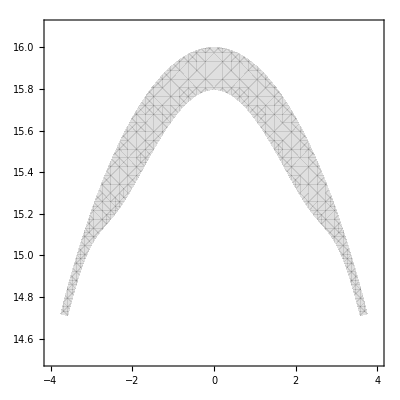

```mathematica
max=18;
cM=Table[Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
me[t1_,t2_]:=Min@Eigenvalues[cM/.{g->1/16,Subscript[t, 1]->t1,Subscript[t, 2]->t2}];
Timing[p18=RegionPlot[me[t1,t2]>0,{t1,-4,4},{t2,14.5,16.1},PlotStyle->Directive[Opacity[0.25],Gray] , BoundaryStyle->None,PerformanceGoal->"Quality"];]
p18
```

```mathematica
p18=-Graphics-;
```

{1632.36,Null}

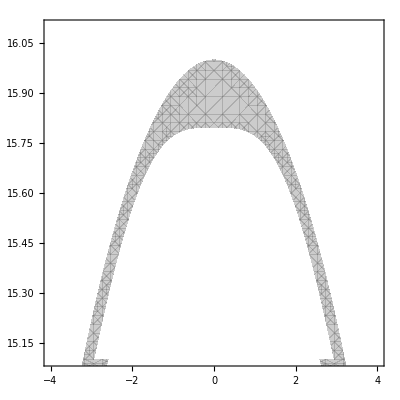

```mathematica
max=20;
cM=Table[Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
me[t1_,t2_]:=Min@Eigenvalues[cM/.{g->1/16,Subscript[t, 1]->t1,Subscript[t, 2]->t2}];
Timing[p20a=RegionPlot[me[t1,t2]>0,{t1,-4,4},{t2,15.1,16.1},PlotStyle->Directive[Opacity[0.4],Gray] , BoundaryStyle->None,PerformanceGoal->"Quality"];]
Show[p20a,p20b]
```

```mathematica
blank=RegionPlot[2<1,{x,-4,4},{y,14.6,16.1}];
```

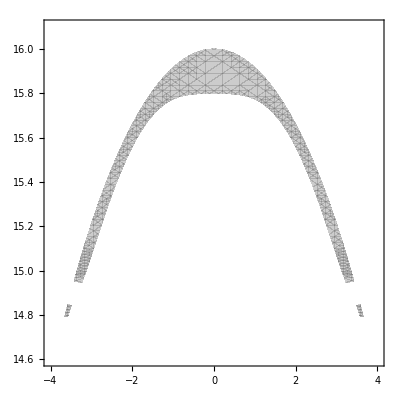

```mathematica
Show[blank,p20a,p20b]
```

```mathematica
p20=-Graphics-;
```

```mathematica
max=20;
cM=Table[Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
me[t1_,t2_]:=Min@Eigenvalues[cM/.{g->1/16,Subscript[t, 1]->t1,Subscript[t, 2]->t2}];
```

```mathematica
Timing[p20bl=RegionPlot[me[t1,t2]>0,{t1,-4,-2},{t2,14.6,15.1},PlotStyle->Directive[Opacity[0.4],Gray] , BoundaryStyle->None];]
```

$Aborted

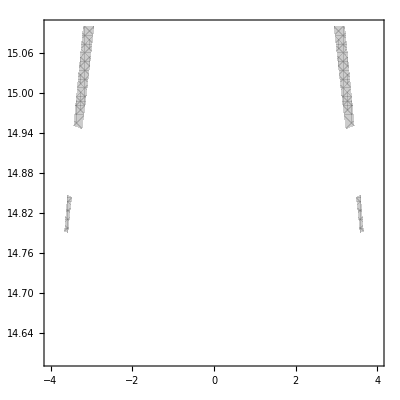

```mathematica
p20b
```

```mathematica
Timing[p20br=RegionPlot[me[t1,t2]>0,{t1,2,4},{t2,14.6,15.1},PlotStyle->Directive[Opacity[0.4],Gray] , BoundaryStyle->None];]
```

```mathematica
p14=RegionPlot[me[t1,t2]>0,{t1,-4,4},{t2,12,14.5},PerformanceGoal->"Quality",PlotStyle->Directive[Opacity[0.25],Gray] , BoundaryStyle->None];
```

```mathematica
blank=RegionPlot[1>2,{t1,-4,4},{t2,8,16}];
```

```mathematica
max=18;
cM=Table[Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
me[t1_,t2_]:=Min@Eigenvalues[cM/.{g->1/10,Subscript[t, 1]->t1,Subscript[t, 2]->t2}]
p10=RegionPlot[me[t1,t2]>0,{t1,-4,4},{t2,8,14},PerformanceGoal->"Quality",PlotStyle->Directive[Opacity[0.25],Gray] , BoundaryStyle->None];
```

```mathematica
exS=ListPlot[{{-3.7482369188729003,14.720000743393971},{-3.4119172853600843,14.961319173504618},{-3.0247677001937308,15.198225380216918},{-2.6566667502369867,15.389646765755115},{-2.305709729195946,15.544873743536902},{-1.970572410414813,15.670140622037625},{-1.6502388341703533,15.770049700256035},{-1.3438820875911617,15.848197891380453},{-1.0508021849275648,15.907504739295138},{-0.7703899022416392,15.950404273997684},{-0.502104014794128,15.978966332256464},{-0.245456112149796,15.994977872832223},{-8.881784197001252*^-16,15.999999999999924},{8.881784197001252*^-16,15.999999999999924},{0.245456112149796,15.994977872832223},{0.502104014794128,15.978966332256464},{0.7703899022416392,15.950404273997684},{1.0508021849275648,15.907504739295138},{1.3438820875911617,15.848197891380453},{1.6502388341703533,15.770049700256035},{1.970572410414813,15.670140622037625},{2.305709729195946,15.544873743536902},{2.6566667502369867,15.389646765755115},{3.0247677001937308,15.198225380216918},{3.4119172853600843,14.961319173504618},{+3.7482369188729003,14.720000743393971}},plotsci,PlotStyle->Darker@Green,Joined->True,InterpolationOrder->2];
```

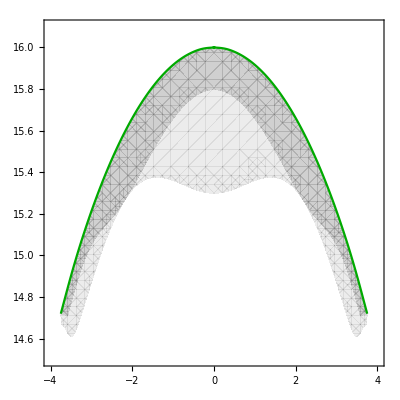
-Graphics-tr Atr A^2

```mathematica
Labeled[Show[p16,p18,exS,plotsci],{"tr A", "tr A^2"},{Bottom,Left},labelsci]
```

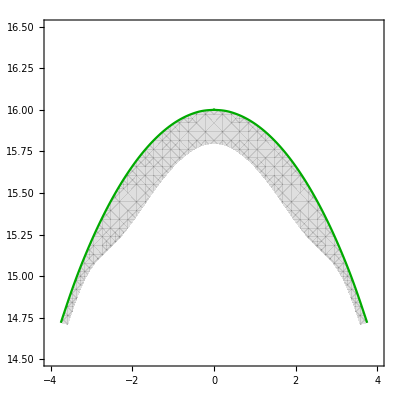
-Graphics-tr Atr A^2

```mathematica
Labeled[Show[p16,exS,plotsci],{"tr A", "tr A^2"},{Bottom,Left},labelsci]
```

```mathematica
data={{0,1/g/.{g->1/14}},{0,1/g/.{g->1/16}},{0,1/g/.{g->1/10}},{-3.7482369188729003,14.720000743393971},{+3.7482369188729003,14.720000743393971},

{-8.881784197001252*^-16,15.999999999999924},{0.245456112149796,15.994977872832223},{0.502104014794128,15.978966332256464},{0.7703899022416392,15.950404273997684},{1.0508021849275648,15.907504739295138},{1.3438820875911617,15.848197891380453},{1.6502388341703533,15.770049700256035},{1.970572410414813,15.670140622037625},{2.305709729195946,15.544873743536902},{2.6566667502369867,15.389646765755115}
};
elements={"g = 1/14", "g = 1/16 (s)", "g = 1/10", "(a-)", "(a+)"};
dataPlot=ListPlot[data,PlotStyle->Darker@Green];
```

```mathematica
labels=MapThread[Text[Style[#1,15,Darker@Green],#2+{0,-0.2}]&,{elements,data}];
```

```mathematica
me[t1_,t2_]:=Min@Eigenvalues[cM/.{g->1/14,Subscript[t, 1]->t1,Subscript[t, 2]->t2}]
```

```mathematica
RegionPlot[me[t1,t2]>0,{t1,-4,4},{t2,0,20},PerformanceGoal->"Quality"]
```

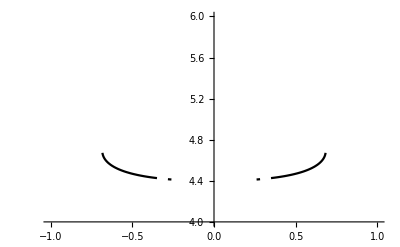

```mathematica
p4a=Plot[Re@sol4[[3]],{Subscript[t, 1],-1,1},PlotRange->{4,6},PlotStyle->Black]
```

```mathematica
p4=Plot[Re@sol4[[4;;6]],{Subscript[t, 1],-1,1},PlotRange->{4,6},PlotStyle->Black];
```

```mathematica
p2=Plot[sol2[[5;;6]],{Subscript[t, 1],-1,1},PlotRange->{1.5,2.5},PlotStyle->Black];
```

```mathematica
p3=Plot[sol3[[5;;6]],{Subscript[t, 1],-1,1},PlotRange->{0,1},PlotStyle->Black];
```

```mathematica
p1=Plot[sol[[5;;6]],{Subscript[t, 1],-1,1},PlotRange->{1,2},PlotStyle->Black];
```

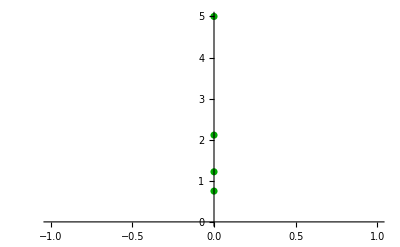

```mathematica
pExact=ListPlot[{{0,(1+72 g/4+√(1+48 g/4)+48 g/4 √(1+48 g/4))/(864 (g/4)^2)/.{g->1}},{0,(1+72 g/4+√(1+48 g/4)+48 g/4 √(1+48 g/4))/(864 (g/4)^2)/.{g->1/2}},{0,(1+72 g/4+√(1+48 g/4)+48 g/4 √(1+48 g/4))/(864 (g/4)^2)/.{g->2}},{0,1/g/.{g->1/5}}},PlotStyle->Darker@Green ]
```

```mathematica
data={{0,(1+72 g/4+√(1+48 g/4)+48 g/4 √(1+48 g/4))/(864 (g/4)^2)/.{g->1}},{0,(1+72 g/4+√(1+48 g/4)+48 g/4 √(1+48 g/4))/(864 (g/4)^2)/.{g->1/2}},{0,(1+72 g/4+√(1+48 g/4)+48 g/4 √(1+48 g/4))/(864 (g/4)^2)/.{g->2}},{0,1/g/.{g->1/5}},{0,1/g/.{g->1/16}},{0,1/g/.{g->1/5}}};
elements={"g = 1", "g = 1/2", "g = 2", "g= 1/5"};
```

```mathematica
dataPlot=ListPlot[data,PlotStyle->Darker@Green];
labels=MapThread[Text[Style[#1,15,Darker@Green],#2+{0,-0.2}]&,{elements,data}];
```

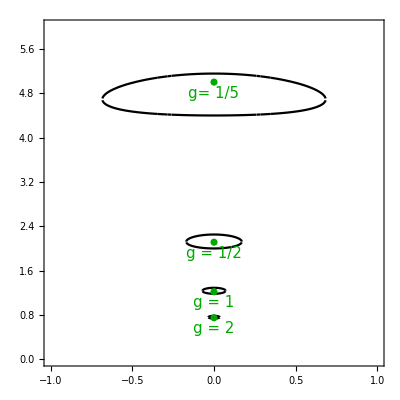
-Graphics-tr A^2tr A

```mathematica
Labeled[Show[{p1,p2,p3,dataPlot,Graphics[labels],p4a,p4},PlotRange->{{-1,1},{0,6}},plotsci,AspectRatio->1,Axes->False],{"tr A^2","tr A"},{Left,Bottom},labelsci]
```

```mathematica
ρ[λ_,g_,a1_,a2_]:=(-1/2 g λ^2-g/4(a1+a2)λ+1/16(8-3a1^2 g-2a1 a2 g - 3 a2^2 g))Sqrt[(λ-a1)(λ-a2)];
```

```mathematica
1.{a1,a2}/.Solve[{(a1+a2)(5a1 g-2 a2 a1 g+ 5 a2^2 g - 8)==0,(a1-a2)^2(3(5 a1^2+6a2 a1 + 5a2^2)g-16) ==256}/.{g->1},{a1,a2}]
```

{{0.-1.31797 ⅈ,0.+1.31797 ⅈ},{0.+1.31797 ⅈ,0.-1.31797 ⅈ},{-1.75225,1.75225},{1.75225,-1.75225},{-3.90782,-3.25516},{-1.91889,1.53095},{-1.04722-1.71729 ⅈ,-1.90485-0.892341 ⅈ},{-1.04722+1.71729 ⅈ,-1.90485+0.892341 ⅈ},{2.15259-0.111006 ⅈ,0.35533-0.633261 ⅈ},{2.15259+0.111006 ⅈ,0.35533+0.633261 ⅈ},{0.16571+1.76959 ⅈ,1.35472-0.306707 ⅈ},{0.16571-1.76959 ⅈ,1.35472+0.306707 ⅈ}}

```mathematica
a1=-1.7522464201635548;
a2=1.7522464201635548;
```

```mathematica
Integrate[I/π ρ[λ,1,a1,a2]λ^2,{λ,a1,a2}]
```

1.21985+5.09871×10^-21 ⅈ

```mathematica
Clear[a1,a2]
```

```mathematica
1.{a1,a2}/.Solve[{(a1+a2)(5a1 g-2 a2 a1 g+ 5 a2^2 g - 8)==0,(a1-a2)^2(3(5 a1^2+6a2 a1 + 5a2^2)g-16) ==256}/.{g->2},{a1,a2}]
```

{{-1.41421,1.41421},{1.41421,-1.41421},{0.-1.1547 ⅈ,0.+1.1547 ⅈ},{0.+1.1547 ⅈ,0.-1.1547 ⅈ},{-3.34766,-2.81334},{-1.54078,1.25253},{-0.963701-1.54469 ⅈ,-1.62242-0.890809 ⅈ},{-0.963701+1.54469 ⅈ,-1.62242+0.890809 ⅈ},{1.666-0.144467 ⅈ,0.261432-0.901227 ⅈ},{1.666+0.144467 ⅈ,0.261432+0.901227 ⅈ},{0.0996398+1.56278 ⅈ,1.08448-0.4156 ⅈ},{0.0996398-1.56278 ⅈ,1.08448+0.4156 ⅈ}}

```mathematica
a1=-1.4142135623730951;
a2=1.4142135623730951;
```

```mathematica
NIntegrate[I/π ρ[λ,2,a1,a2] λ^2,{λ,a1,a2}]
```

0.75+0. ⅈ

```mathematica
Clear[a1,a2]
```

```mathematica
1.{a1,a2}/.Solve[{(a1+a2)(5a1 g-2 a2 a1 g+ 5 a2^2 g - 8)==0,(a1-a2)^2(3(5 a1^2+6a2 a1 + 5a2^2)g-16) ==256}/.{g->1/2},{a1,a2}]
```

{{0.-1.48133 ⅈ,0.+1.48133 ⅈ},{0.+1.48133 ⅈ,0.-1.48133 ⅈ},{-2.20477,2.20477},{2.20477,-2.20477},{-4.66602,-3.88903},{2.63518,-0.390892},{2.96107,1.3601},{-2.40557,1.93488},{-1.19995-1.79295 ⅈ,-2.37107-0.819637 ⅈ},{-1.19995+1.79295 ⅈ,-2.37107+0.819637 ⅈ},{0.295343+1.95801 ⅈ,1.80663-0.155373 ⅈ},{0.295343-1.95801 ⅈ,1.80663+0.155373 ⅈ}}

```mathematica
a1=-2.204767957878135;
a2=-a1;
```

```mathematica
NIntegrate[I/π ρ[λ,1/2,a1,a2] λ^2,{λ,a1,a2}]
```

2.11261+0. ⅈ

```mathematica
1.{a1,a2}/.Solve[{(a1+a2)(5a1 g-2 a2 a1 g+ 5 a2^2 g - 8)==0,(a1-a2)^2(3(5 a1^2+6a2 a1 + 5a2^2)g-16) ==256},{a1,a2}]/.{g->1/5}
```

{{0.-1.67721 ⅈ,0.+1.67721 ⅈ},{0.+1.67721 ⅈ,0.-1.67721 ⅈ},{-3.07891,3.07891},{3.07891,-3.07891},{-6.11222,-5.17296},{3.58264,-1.50401},{-3.31632,2.76547},{4.44945,2.97375},{-1.58091-1.52001 ⅈ,-3.42493-0.579393 ⅈ},{-1.58091+1.52001 ⅈ,-3.42493+0.579393 ⅈ},{0.63686-2.01457 ⅈ,2.83689-0.050097 ⅈ},{0.63686+2.01457 ⅈ,2.83689+0.050097 ⅈ}}

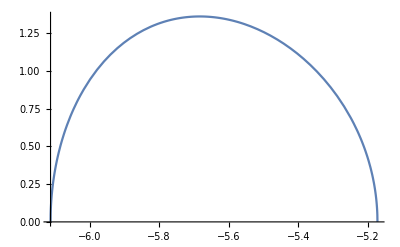

```mathematica
Plot[I/π ρ[λ,1/5,-6.11221878084384,-5.172961129605843],{λ,-6.11221878084384,-5.172961129605843}]
```

This step should take ~1 min for max ~ 50

```mathematica
cM=Table[g^(j+k)Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
jm=4;
res=1/10;
dat=Table[{j*res,detM=Det[cM/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
```

```mathematica
Min@Eigenvalues[cM/.{g->1/20,Subscript[t, 2]->11.}]
```

-6.39456×10^-8

```mathematica
l6=ListPlot[{down6,up6},Joined->True,InterpolationOrder->2,PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Gray,Opacity[0.3]],PerformanceGoal->"Quality",Evaluate@plotsci]
```

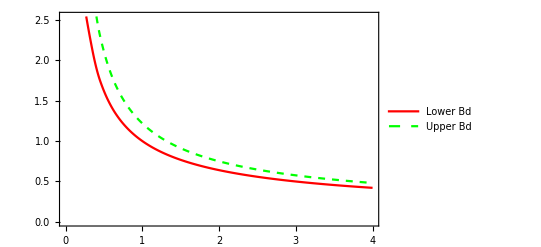
-Graphics-tr M^2g

```mathematica
up=Transpose@{dat[[;;,1]],dat[[;;,2,-4]]};
down=Transpose@{dat[[;;,1]],dat[[;;,2,-5]]};
Labeled[Show[ListPlot[{down,up},Joined->True,InterpolationOrder->2,PlotStyle->{Red,{Green,Dashed}},PlotLegends->{"Lower Bd"," Upper Bd"}],Evaluate@plotsci],{"tr M^2","g"},{Left,Bottom},labelsci]
```

```mathematica
Subscript[t, 0]=1;Subscript[t, 1]=0;max=30; (* choose an even number for compatibility with cM *)
Do[
Subscript[t, k+2]=0;
Subscript[t, k+3]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]+Subscript[t, k+1])],{k,Range[1,max-3,2]}
];
```

```mathematica
cM=Table[g^(j+k)Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
jm=4;
res=1/10;
dat=Table[{j*res,detM=Det[cM/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
```

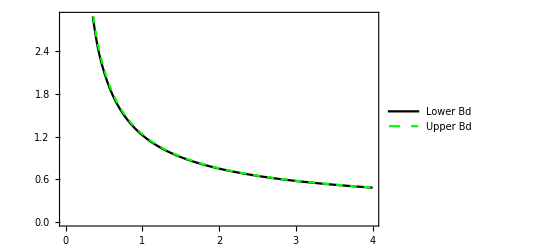
-Graphics-tr M^2g

```mathematica
up2=Transpose@{dat[[;;,1]],dat[[;;,2,-4]]};
down2=Transpose@{dat[[;;,1]],dat[[;;,2,-5]]};
Labeled[Show[ListPlot[{down2,up2},Joined->True,InterpolationOrder->2,PlotStyle->{Black,{Green,Dashed}},PlotLegends->{"Lower Bd"," Upper Bd"}],Evaluate@plotsci],{"tr M^2","g"},{Left,Bottom},labelsci]
```

Now we do the case with SSB

```mathematica
Subscript[t, 0]=1;Subscript[t, 1]=0.1;max=20; (* choose an even number for compatibility with cM *)
Do[
Subscript[t, k+3]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]+Subscript[t, k+1])],{k,Range[0,max-3,1]}
];
```

```mathematica
max=10;
```

```mathematica
cM=Table[g^(j+k)Subscript[t, j+k],{j,0,max/2},{k,Range[0,max/2]}];
jm=1;
res=1/50.;
dat=Table[{j*res,detM=Det[cM/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
```

```mathematica
NMaximize[]
```

```mathematica
2 Sqrt[2]/3 ((a+b)/Sqrt[2])^3//Expand
```

a^3/3+a^2 b+a b^2+b^3/3

```mathematica
dat[[1]]
```

{1/50,{-89.8928,-3.56708,-2.40402,-1.65591,-0.747824,0.477468,0.572783,0.908973,4.80589,50.0533,151.948}}

```mathematica
Subscript[t, 0]=1;Subscript[t, 1]=0;max=19;(*Odd number*)
Do[
Subscript[t, k+2]=0;(** this should now be a parameter **)
Subscript[t, k+3]=Simplify[1/g(Sum[-Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]-Subscript[t, k+1])],{k,Range[1,max,2]}
];
```

```mathematica
cM=Table[g^(j+k)Subscript[t, j+k],{j,Range[0,max+1,2]},{k,Range[0,max+1,2]}];
jm=5;
res=1/10;
```

```mathematica
dat=Table[{j*res,detM=Det[cM/.{g->1+j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
up=Transpose@{dat[[;;,1]],dat[[;;,2,-3]]};
down=Transpose@{dat[[;;,1]],dat[[;;,2,-4]]};
```

$Aborted

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {Symbol[],Symbol[]} cannot be transposed.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {Symbol[],Symbol[]} cannot be transposed.

```mathematica
Subscript[t, 0]=1;Subscript[t, 1]=0;max=19;(*Odd number*)
Do[
Subscript[t, k+2]=0;
Subscript[t, k+3]=Simplify[1/g(Sum[Subscript[t, l] Subscript[t, k-l-1],{l,0,k-1}]-Subscript[t, k+1])],{k,Range[1,max,2]}
];
cM=Table[If[OddQ[j+k],0,g^(j+k)Subscript[t, j+k]],{j,Range[0,max+1]},{k,Range[0,max+1]}];
```

```mathematica
OddQ[3]
```

True

```mathematica
jm=5;
res=1/80;
d=4;
dat6=Table[{j*res,detM=Det[cM[[;;d,;;d]]/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
PrependTo[dat6,{0,ConstantArray[1,Length[dat[[1,2]]]]}];
```

{-5,-4,-3,-2,-1}

```mathematica
d=5;
dat7=Table[{j*res,detM=Det[cM[[;;d,;;d]]/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
PrependTo[dat7,{0,ConstantArray[1,Length[dat[[1,2]]]]}];
```

```mathematica
d=6;
dat8=Table[{j*res,detM=Det[cM[[;;d,;;d]]/.{g->j*res}]/.{Subscript[t, 2]->t2};Normal@NSolve[detM==0,t2,Reals][[;;,1,2]]},{j,1,jm/res}];
PrependTo[dat8,{0,ConstantArray[1,Length[dat[[1,2]]]]}];
```

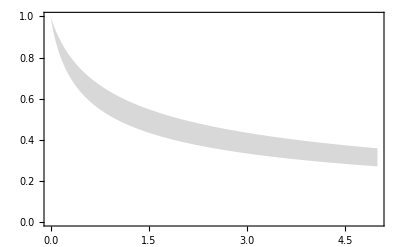

```mathematica
up6=Transpose@{dat6[[;;,1]],dat6[[;;,2,-1]]};
down6=Transpose@{dat6[[;;,1]],dat6[[;;,2,-2]]};
l6=ListPlot[{down6,up6},Joined->True,InterpolationOrder->2,PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Gray,Opacity[0.3]],PerformanceGoal->"Quality",Evaluate@plotsci]
```

```mathematica
dat6[[41,2]]
```

{-1.61803,0,0.618034}

```mathematica
Eigenvalues[cM[[;;3,;;3]]/.{g->1,Subscript[t, 2]->0.516}]
```

{1.31891,0.516,0.165094}

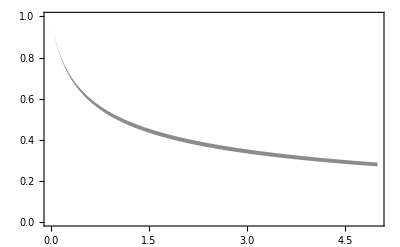

```mathematica
up7=Transpose@{dat7[[;;,1]],dat7[[;;,2,-1]]};
down7=Transpose@{dat7[[;;,1]],dat7[[;;,2,-2]]};
l7=ListPlot[{down7,up7},Joined->True,InterpolationOrder->2,PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Gray,Opacity[0.9]],PerformanceGoal->"Quality",Evaluate@plotsci]
```

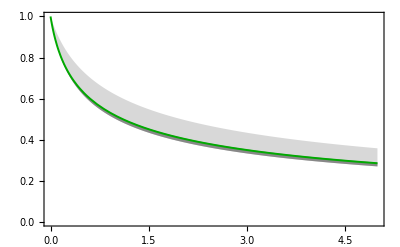
-Graphics-tr M^2g

```mathematica
Labeled[Show[l6,l7,Plot[{c2[x]},{x,0,5},PlotRange->{0,1},PlotStyle->{{Darker@Green,Thickness[0.0035]}},GridLines->{{0,-1/12}}]],{"tr M^2","g"},{Left,Bottom},labelsci]
```